# Introduction to Machine Learning: Gradient Descent

This notebook will walk through implementing gradient descent from scratch. We will use this to fit a line to data, such that we only have two parameters to learn. Extending to more dimensions is easy, but hard to visualize.

## Generate the Data

### Create

The data will consist of (x,y) pairs. The range of x will be from 0 to 10.

```mathematica
XData = Table[i,{i,0,10}]
```

{0,1,2,3,4,5,6,7,8,9,10}

We then will pick the y values to follow the equation y(x) = 8 - 0.8 x. However, we add a little noise so that the line is not perfect.

```mathematica
YData = Table[(1+RandomVariate[NormalDistribution[]]/10)*(8-0.8XData[[i]]), {i,1,Length[XData]}]
```

{7.35086,7.15602,6.41668,5.9065,4.70057,4.41449,2.70893,2.63439,1.7671,0.754668,0.}

Now combine the x and y columns into (x,y) pairs

```mathematica
pData=Table[{XData[[i]],YData[[i]]},{i,1,Length[XData]}];
pData//TableForm
```

0 | 7.35086
1 | 7.15602
2 | 6.41668
3 | 5.9065
4 | 4.70057
5 | 4.41449
6 | 2.70893
7 | 2.63439
8 | 1.7671
9 | 0.754668
10 | 0.

### Visualize

Now plot the data so that we can see what we are trying to fit

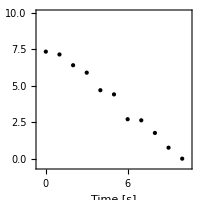

```mathematica
DataPlot = ListPlot[pData,
BaseStyle->FontSize->14,
Frame->True,
FrameStyle->Black,
PlotRange->{{-0.5,10.5},{-0.5,10}},
AspectRatio->1,
PlotStyle->{Black,PointSize[Large]},
FrameLabel->{"Time [s]", "Distance [m]"},
ImageSize->{200,200}
]
```

## Function definitions

### Our prediction

First we have to define a function that we think may fit the data. In this case, it looks like a line should do. The we will use the standard form of y = m*x +b, and define m as a_0 and  b as a_1. Our goal is to learn the values of a_0 and a_1. For a given x, a0, and a1, we then make a prediction for what the y-value should be.

```mathematica
OurPrediction[x_,a0_,a1_]:=a0+a1*x
```

### Loss function

#### Errors

Once we have our prediction, we need to decide if it fits the data well or not. Make a function that for a given a_0 and a_1 will scan through each of the given x-values and subtract the TRUE y-value from our prediction

```mathematica
Errors[a0_,a1_]:=Table[YData[[i]]-OurPrediction[XData[[i]],a0,a1],{i,1,Length[XData]}]
```

Lets see if that worked. Plot a test prediction versus the data.

```mathematica
testa0=1;testa1=2;
```

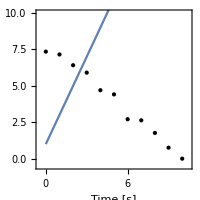

```mathematica
Show[DataPlot,
Plot[OurPrediction[x,testa0,testa1],{x,0,10}]
]
```

```mathematica
Errors[testa0,testa1]
```

{6.35086,4.15602,1.41668,-1.0935,-4.29943,-6.58551,-10.2911,-12.3656,-15.2329,-18.2453,-21.}

Note that this is only a function of a_0 and a_1.

#### Mean squared error

By putting a positive slope, we see that some of the errors are positive and some are negative. How do we decide if the fit is good or not? If we take the mean of these numbers, the positive and negative will cancel out. That doesn’t seem good! Having a big negative error and big positive error should not be as good as having small errors. To fix this, lets take the square of all of the errors and then take the mean. We can then look to find a_0 and a_1 which give us the smallest mean squared error.

```mathematica
MeanSquaredError [a0_,a1_]:= 1/Length[XData]*Sum[Errors[a0,a1][[i]]^2,{i,1,Length[XData]}]
```

Note that we have summed over all of the actual data points, so this is only a function of a_0 and a_1. Now lets make a plot to visualize how the score (the mean squared error) changes over a range of the parameters. We know the answer should be around a_0= -0.8 and a_1 = 8.

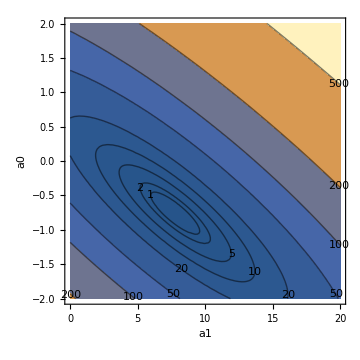

```mathematica
ContourPlot[MeanSquaredError [a0,a1],
{a0,0,20},{a1,-2,2},
PlotRange->{{0,20},{-2,2},All},
Contours->{1,2, 5,10,20,50,100,200,500,1000},
ContourShading->Automatic,
ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),
BaseStyle->FontSize->14,
Frame->True,
FrameStyle->Black,
PlotRange->{{-0.5,10.5},{-0.5,10}},
AspectRatio->1,
ImageSize->Medium,
FrameLabel->{"a1", "a0"}
]
```

## Finding the minimum

### Analytic solution

The best fit will then be when the mean squared error is minimized. From calculus, we know that a critical point occurs when the derivative is 0. Let us then get the gradient and solve for when it = 0.

```mathematica
MSE[a0,a1]=Simplify[MeanSquaredError [a0,a1]]
```

21.8962+a0^2-24.4012 a1+35. a1^2+a0 (-7.96549+10. a1)

```mathematica
MyGrad[a0_,a1_]=Grad[MSE[a0,a1],{a0,a1}]
```

{-7.96549+2 a0+10. a1,-24.4012+10. a0+70. a1}

```mathematica
ExactAnswer = Solve[MyGrad[a0,a1]=={0,0},{a0,a1}]
```

{{a0→7.83931,a1→-0.771312}}

This is the exact answer that we are looking for.

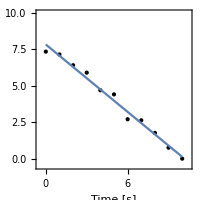

```mathematica
Show[DataPlot,
Plot[7.839306791304646+-0.7713119102578935*x,{x,0,10}]
]
```

### Gradient Descent

What if the data we are trying to fit (or the model we are using) is too complicated to solve easily like this? We can start with a random guess for the right answer, and then use the gradient to show us the slope of the point we are at. We can then take a small step in that direction. If we repeat this process, we should continualy step towards a minimum. Let’s start with a bad guess, and see how this works.

```mathematica
MyPoint={1,2}
LearningRate=0.005
```

{1,2}

0.005

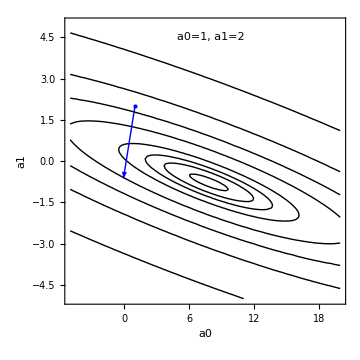

```mathematica
Show[{
ContourPlot[MeanSquaredError [a0,a1],
{a0,-5,20},{a1,-5,5},
PlotRange->{{-5,20},{-5,5},All},
Contours->{1,5,10,20,50,100,200,500},
ContourShading->None,
BaseStyle->FontSize->14,
Frame->True,
FrameStyle->Black,
PlotRange->{{-0.5,10.5},{-0.5,10}},
AspectRatio->1,
ImageSize->Medium,
FrameLabel->{"a0", "a1"}
],
Graphics[{Blue, Arrow[{MyPoint,-.005*MyGrad[MyPoint[[1]],MyPoint[[2]]]}]}],
Graphics[Text["a0="<>ToString[MyPoint[[1]]]<>", a1="<>ToString[MyPoint[[2]]],{8,4.5}]],
Graphics[{Blue,PointSize[Large],Point[MyPoint]}]
}
]
```

The arrow shows us the direction that we need to step, and the size is proportional to how far we should step (multiplied by 0.005). Let’s update our point and repeat the process.

```mathematica
MyPoint=MyPoint - LearningRate*MyGrad[MyPoint[[1]],MyPoint[[2]]]
```

{0.929827,1.37201}

We took a small step

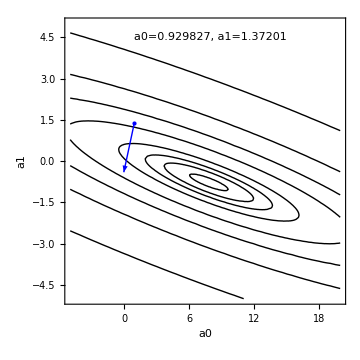

```mathematica
Show[{
ContourPlot[MeanSquaredError [a0,a1],
{a0,-5,20},{a1,-5,5},
PlotRange->{{-5,20},{-5,5},All},
Contours->{1,5,10,20,50,100,200,500},
ContourShading->None,
BaseStyle->FontSize->14,
Frame->True,
FrameStyle->Black,
PlotRange->{{-0.5,10.5},{-0.5,10}},
AspectRatio->1,
ImageSize->Medium,
FrameLabel->{"a0", "a1"}
],
Graphics[{Blue, Arrow[{MyPoint,-.005*MyGrad[MyPoint[[1]],MyPoint[[2]]]}]}],
Graphics[Text["a0="<>ToString[MyPoint[[1]]]<>", a1="<>ToString[MyPoint[[2]]],{8,4.5}]],
Graphics[{Blue,PointSize[Large],Point[MyPoint]}]
}
]
```

Update again

```mathematica
MyPoint=MyPoint -LearningRate*MyGrad[MyPoint[[1]],MyPoint[[2]]]
```

{0.891756,0.967319}

We see that this is taking us in the right direction, but going slow. Let’s repeat the process a large number of times.

```mathematica
Do[
MyPoint=MyPoint-LearningRate*MyGrad[MyPoint[[1]],MyPoint[[2]]],
{i,1,2000}]
MyPoint
```

{7.81341,-0.767583}

This is very close to what our exact answer is

```mathematica
ExactAnswer
```

{{a0→7.83931,a1→-0.771312}}

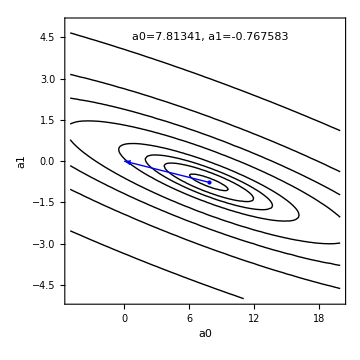

```mathematica
Show[{
ContourPlot[MeanSquaredError [a0,a1],
{a0,-5,20},{a1,-5,5},
PlotRange->{{-5,20},{-5,5},All},
Contours->{1,5,10,20,50,100,200,500},
ContourShading->None,
BaseStyle->FontSize->14,
Frame->True,
FrameStyle->Black,
PlotRange->{{-0.5,10.5},{-0.5,10}},
AspectRatio->1,
ImageSize->Medium,
FrameLabel->{"a0", "a1"}
],
Graphics[{Blue, Arrow[{MyPoint,-.005*MyGrad[MyPoint[[1]],MyPoint[[2]]]}]}],
Graphics[Text["a0="<>ToString[MyPoint[[1]]]<>", a1="<>ToString[MyPoint[[2]]],{8,4.5}]],
Graphics[{Blue,PointSize[Large],Point[MyPoint]}]
}
]
```

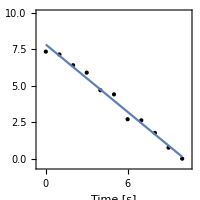

```mathematica
Show[{
ListPlot[pData,
BaseStyle->FontSize->14,
Frame->True,
FrameStyle->Black,
PlotRange->{{-0.5,10.5},{-0.5,10}},
AspectRatio->1,
PlotStyle->{Black,PointSize[Large]},
FrameLabel->{"Time [s]", "Distance [m]"},
ImageSize->{200,200}
],
Plot[MyPoint[[1]]+MyPoint[[2]]*x,{x,0,10}]
}
]
```

This shows that we  can use gradient descent to find the minimums of loss functions. This technique will allow us to use machine learning on much harder datasets.

## Automate the process and make graphs

```mathematica
MyPoint={0,0}
Do[
mygraph = GraphicsRow[
{
Show[{
ContourPlot[MeanSquaredError [a0,a1],
{a0,-5,20},{a1,-5,5},
PlotRange->{{-5,20},{-5,5},All},
Contours->{1,5,10,20,50,100,200,500},
ContourShading->None,
(*ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),*)
BaseStyle->FontSize->14,
Frame->True,
FrameStyle->Black,
PlotRange->{{-0.5,10.5},{-0.5,10}},
AspectRatio->1,
ImageSize->Medium,
FrameLabel->{"a0", "a1"}
],
Graphics[{Darker[Green],Arrow[{MyPoint,MyPoint-.5*MyGrad[MyPoint[[1]],MyPoint[[2]]]}]}],
Graphics[{Darker[Green],PointSize[Large],Point[MyPoint]}],
Graphics[Text["a0="<>ToString[MyPoint[[1]]]<>", a1="<>ToString[MyPoint[[2]]],{8,4.5}]]
}
],
Show[{
ListPlot[pData,
BaseStyle->FontSize->14,
Frame->True,
FrameStyle->Black,
PlotRange->{{-0.5,10.5},{-0.5,10}},
AspectRatio->1,
PlotStyle->{Black,PointSize[Large]},
FrameLabel->{"Time [s]", "Distance [m]"}
],
Plot[MyPoint[[1]]+MyPoint[[2]]*x,{x,0,10}]
}
]
}
];
If[i<10,
Export["~/Desktop/GradDescent/GradDescent_00"<>ToString[i]<>".png",mygraph];];
If[10≤i<100,
Export["~/Desktop/GradDescent/GradDescent_0"<>ToString[i]<>".png",mygraph];];
If[i>=100,
Export["~/Desktop/GradDescent/GradDescent_"<>ToString[i]<>".png",mygraph];];
MyPoint+=-.02*MyGrad[MyPoint[[1]],MyPoint[[2]]];
(*Print[MyPoint]*)
,{i,0,300}
]
```

{0,0}

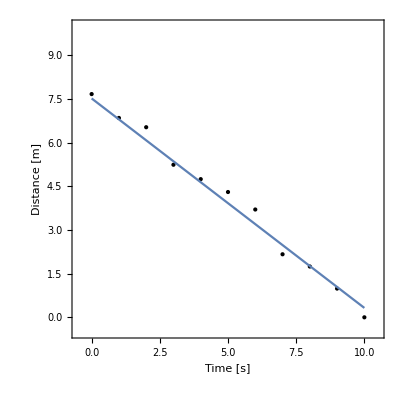

```mathematica
Show[{
ListPlot[pData,
BaseStyle->FontSize->14,
Frame->True,
FrameStyle->Black,
PlotRange->{{-0.5,10.5},{-0.5,10}},
AspectRatio->1,
PlotStyle->{Black,PointSize[Large]},
FrameLabel->{"Time [s]", "Distance [m]"}
],
Plot[MyPoint[[1]]+MyPoint[[2]]*x,{x,0,10}]
}]
```